```mathematica
mass = 1;
rs=2;
close=10^-10;
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,2},Mesh->False];
```

```mathematica
theta[r0_,r1_]:=NIntegrate[1/(r^2 √(1/b^2-(1-rs/r)1/r^2)),{r,r0,r1}]
```

```mathematica
n[z_]:=IntegerPart[z]
zf[z_]:=FractionalPart[z]
```

```mathematica
r[z_]:=If[z<0.5,u1-2z*(u1-r3),2(z-0.5)(u2-r3)+r3]
```

```mathematica
accphi[z_]:=If[z<0.5,theta[u1,u1-2z(u1-r3)+close],theta[u1,r3+close]-theta[r3+close,2(z-0.5)(u2-r3)+r3+close]]
```

```mathematica
x[z_]:=Cos[accphi[z]]r[z]
y[z_]:=Sin[accphi[z]]r[z]
```

```mathematica
fb[theta_,r_,rs_]:=(r Sin[theta])/(√(1-rs/r))
```

```mathematica
u1=14
u2=30
```

14

30

```mathematica
b=5.270690658034941
```

5.27069

```mathematica
angle=Pi/12
rst=20;
r3=Last@@Last@@NSolve[b==r/(√(1-rs/r)),r]
N[b]
```

π/12

3.33391

5.27069

```mathematica
b:=fb[angle,rst,rs];
```

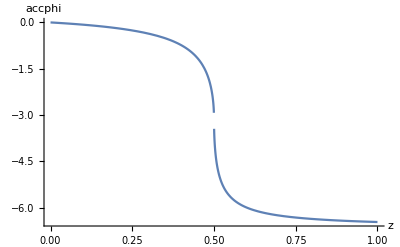

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"},PlotRange->All]
```

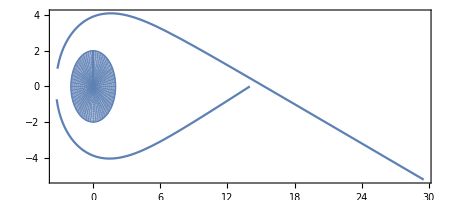

```mathematica
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,graph,PlotRange->All]
```

```mathematica
4
```

4

```mathematica
theta[u1,r3+close]
```

-2.64172

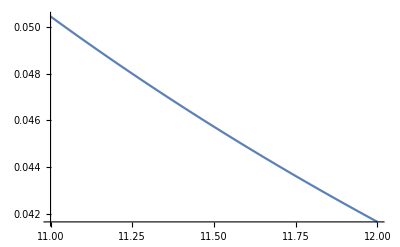

```mathematica
Plot[1/(r^2 √(1/b^2-(1-rs/r)1/r^2)),{r,11,12}]
```

```mathematica
accphi[1]/Degree
```

-308.059

```mathematica
r3
```

3.69641

```mathematica
u1
```

20

```mathematica
N[70*Pi/180]
```

1.22173

```mathematica
theta[12,2000000]
```

0.469615

```mathematica
NSolve[1/b^2-(1-rs/r)1/r^2==0]
```

{{r→-10.8803},{r→8.78885},{r→2.09149}}

```mathematica
NSolve[b==r/(√(1-rs/r)),r]
```

{{r→8.78885},{r→2.09149}}

```mathematica
b=10
```

10

```mathematica
10
```

```mathematica
r3=8.788850662499737
```

8.78885

```mathematica
r3=2.0914884844131674
```

2.09149

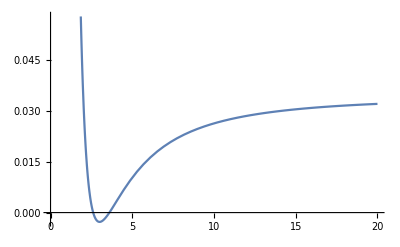

```mathematica
Plot[1/b^2-(1-rs/r)1/r^2,{r,0,20}]
```